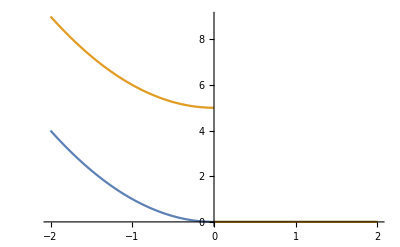

```mathematica
f1[x_]:=Piecewise[{{0 x, x>=0}, {x, x<0}}];
f2[x_]:=Piecewise[{{0, x>=0}, {Sqrt[x^2+5], x<0}}];
Plot[{f1[x]^2,f2[x]^2}, {x,-2,2}]
```